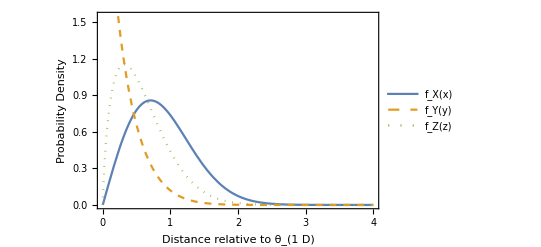

```mathematica
fX[x_]:=2*x*Exp[-x^2/theta^2]
fYX[x_,y_]:=2(x-y)/x^2
fY[y_]:=2*Sqrt[Pi]/theta*Erfc[y/theta]-2*y/theta*Gamma[0,y^2]
fZ[z_]:=2*z/theta^2*Gamma[0,z^2]

theta=1

Integrate[]

Plot[{fX[x],fY[x],fZ[x]},{x,0,4},PlotStyle-> {Line, Dashed,Dotted}, Frame-> True,FrameLabel-> {Style["Distance relative to θ_(1  D)", Bold, 12],Style["Probability Density", Bold, 12] }, RotateLabel->True, PlotLegends-> Placed[{"f_X(x)", "f_Y(y)","f_Z(z)"},Center]]
```

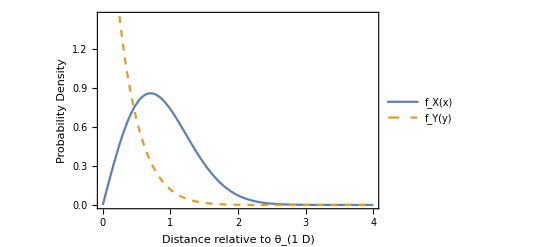

```mathematica
Plot[{fX[x],fY[x]},{x,0,4},PlotStyle-> {Line, Dashed}, Frame-> True,FrameLabel-> {Style["Distance relative to θ_(1  D)", Bold, 12],Style["Probability Density", Bold, 12] }, RotateLabel->True, PlotLegends-> Placed[{"f_X(x)", "f_Y(y)"},Center]]
```

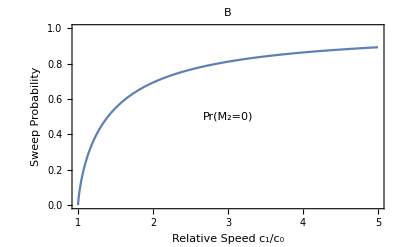

```mathematica
Plot[(c-1)*Log[1+1/(c-1)],{c,1,5},PlotRange->{0,1}, Frame-> True, FrameLabel-> {"Relative Speed c_1/c_0", "Sweep Probability"}, RotateLabel->True,  PlotLegends->Placed["Pr(M_2=0)",Center],PlotLabel->"B"]
```

```mathematica
gamma2[c_]:=(c-1)/1
delta[c_]:=c/(c+1)
arci[c_]:=2*ArcCot[Sqrt[1+gamma2[c]]]/Sqrt[1+gamma2[c]]
```

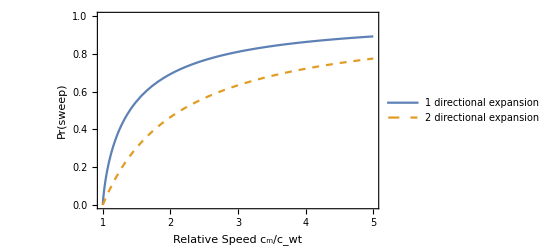

```mathematica
Plot[{(c-1)*Log[1+1/(c-1)],gamma2[c]*(arci[c]+Log[delta[c]])},{c,1,5}, PlotStyle-> {Line, Dashed}, PlotRange->{0,1}, Frame-> True, FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True, PlotLegends->Placed[{"1 directional expansion","2 directional expansion"},Center]]
```

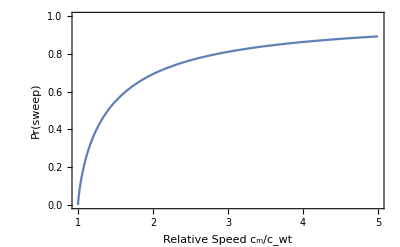

```mathematica
Plot[{(c-1)*Log[1+1/(c-1)],gamma2[c]*(arci[c]+Log[delta[c]])},{c,1,5}, PlotStyle-> {Line, Dashed}, PlotRange->{0,1}, Frame-> True, FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True]
```